```mathematica
PacletInstall["SetReplace"]
```

PacletObject[…]

```mathematica
<<SetReplace`
```

```mathematica
SetReplace[{1,2,5,3,6},{a_,b_}:> {a+b}]
```

{5,3,6,3}

```mathematica
ResourceFunction["WolframModel"][{{x,y}}->{{x,y},{y,z}},{{1,2}},2,"StatesList"]
```

{{{1,2}},{{1,2},{2,3}},{{1,2},{2,4},{2,3},{3,5}}}

Run a Wolfram model for 10 generations, and visualize the result of the final state:

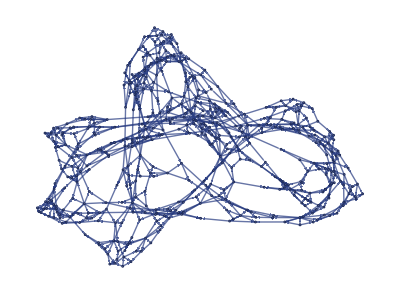

```mathematica
ResourceFunction["WolframModel"][{{x,y},{x,z}}->{{x,z},{x,w},{y,w},{z,w}},{{0,0},{0,0}},10,"FinalStatePlot"]
```

This is example of the of Wolfram Model implemented for SetReplace video by Max.

```mathematica
maxM = ResourceFunction["WolframModel"][{{a,b,c},{d,a,e}}->{{e,b,c},{b,a,d}},{{1,2,3},{2,4,5},{4,6,7}},10]
```

WolframModelEvolutionObject[…]

```mathematica
maxM[4]
```

{{5,6,7},{1,4,6},{4,2,3}}

```mathematica
maxM["CausalGraph"]
```

-Graphics-

# Arithmetic Set Substitution System:

```mathematica
arithmeticEvolution = WolframModel[<|"PatternRules" -> {a_,b_}:> {a+b,a-b,a+b}|>,
{2,8,2,5,2},<|"MaxEvents"-> 8|>]
```

WolframModelEvolutionObject[…]

```mathematica
arithmeticEvolution[[1]]
```

<|Version→2,Rules→<|PatternRules→{a_,b_}:>{a+b,a-b,a+b}|>,MaxCompleteGeneration→2,TerminationReason→MaxEvents,AtomLists→{2,8,2,5,2,10,-6,10,7,-3,7,12,-8,12,4,-16,4,4,10,4,19,-5,19,4,-20,4,-12,20,-12},EventRuleIDs→{0,1,1,1,1,1,1,1,1},EventInputs→{{},{1,2},{3,4},{5,6},{7,8},{9,10},{11,12},{13,14},{15,16}},EventOutputs→{{1,2,3,4,5},{6,7,8},{9,10,11},{12,13,14},{15,16,17},{18,19,20},{21,22,23},{24,25,26},{27,28,29}},EventGenerations→{0,1,1,2,2,2,3,3,3}|>

```mathematica
arithmeticEvolution["Properties"]
```

{EvolutionObject,FinalState,FinalStatePlot,StatesList,StatesPlotsList,EventsStatesPlotsList,AllEventsStatesEdgeIndicesList,AllEventsStatesList,GenerationEdgeIndices,Generation,StateEdgeIndicesAfterEvent,StateAfterEvent,TotalGenerationsCount,PartialGenerationsCount,GenerationsCount,GenerationComplete,AllEventsCount,GenerationEventsCountList,GenerationEventsList,FinalDistinctElementsCount,AllEventsDistinctElementsCount,VertexCountList,EdgeCountList,FinalEdgeCount,AllEventsEdgesCount,AllEventsGenerationsList,ExpressionsEventsGraph,CausalGraph,LayeredCausalGraph,TerminationReason,AllEventsRuleIndices,AllEventsList,EventsStatesList,EdgeCreatorEventIndices,EdgeDestroyerEventsIndices,EdgeDestroyerEventIndices,EdgeGenerationsList,FeatureAssociation,FeatureVector,ExpressionsSeparation,MultiwayQ,Properties,Version,Rules,CompleteGenerationsCount,AllEventsEdgesList}

```mathematica
arithmeticEvolution["StateAfterEvent",2]
```

{2,10,-6,10,7,-3,7}

```mathematica
arithmeticEvolution["ExpressionsEventsGraph"]
```

-Graphics-

```mathematica
arithmeticEvolution["ExpressionsEventsGraph",VertexLabels->Automatic]
```

-Graphics-

```mathematica
arithmeticEvolution["ExpressionsEventsGraph",VertexLabels->"Name"]
```

-Graphics-

# WolframModelPlot

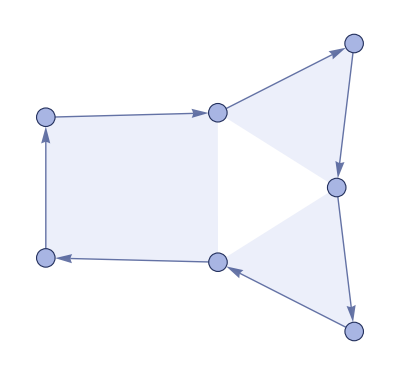

```mathematica
WolframModelPlot[{{1,2,3},{3,4,5},{5,6,7,1}}]
```

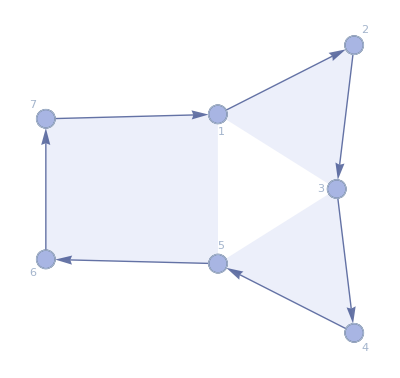

```mathematica
WolframModelPlot[{{1,2,3},{3,4,5},{5,6,7,1}},VertexLabels->Automatic]
```

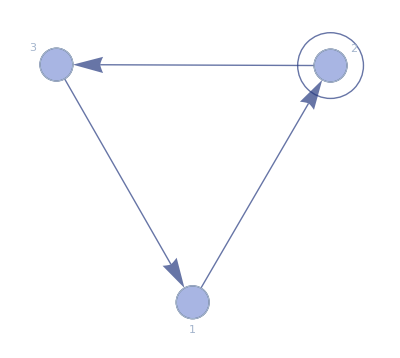

```mathematica
WolframModelPlot[{{1,2},{2},{2,3},{3,1}},VertexLabels->Automatic]
```

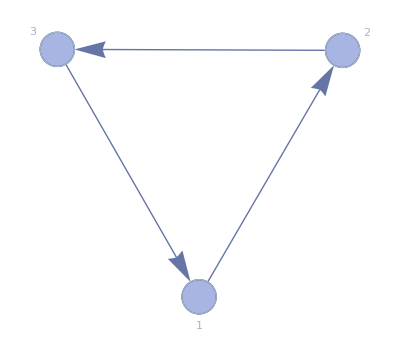

```mathematica
WolframModelPlot[{{1,2},{2,3},{3,1}},VertexLabels->Automatic]
```

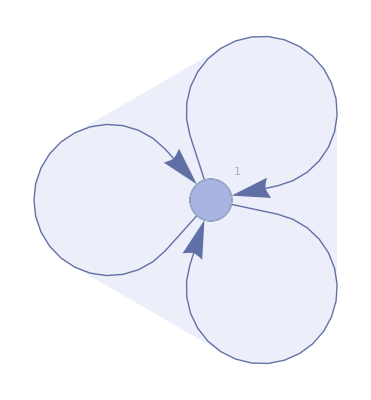

```mathematica
WolframModelPlot[{{1,1,1,1}},VertexLabels->Automatic]
```

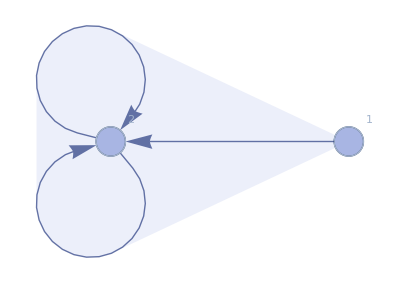

```mathematica
WolframModelPlot[{{1,2,2,2}},VertexLabels->Automatic]
```

# Atom - Preserving Wolfram Models

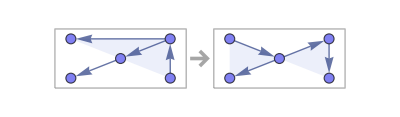

```mathematica
RulePlot[WolframModel[{{1,2,3},{4,1,5}}->{{5,2,3},{2,1,4}}]]
```

```mathematica
atomPreservingEvolution=WolframModel[{{1,2,3},{4,1,5}}->{{5,2,3},{2,1,4}},
{{1,2,3},{2,4,5},{4,6,7}},<|"MaxEvents"->10|>]
```

WolframModelEvolutionObject[…]

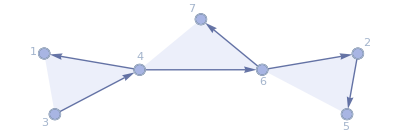

```mathematica
atomPreservingEvolution["FinalStatePlot",VertexLabels->Automatic]
```

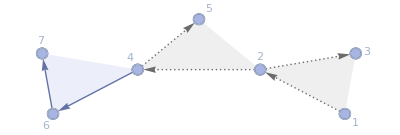
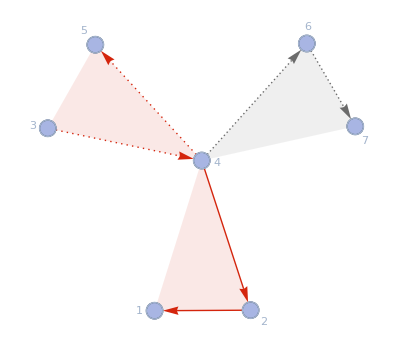
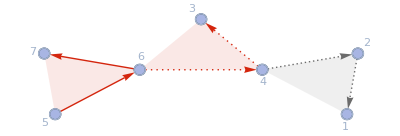
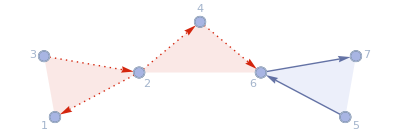
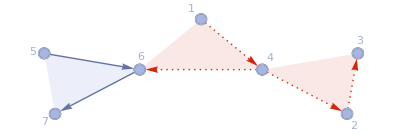
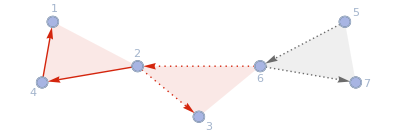
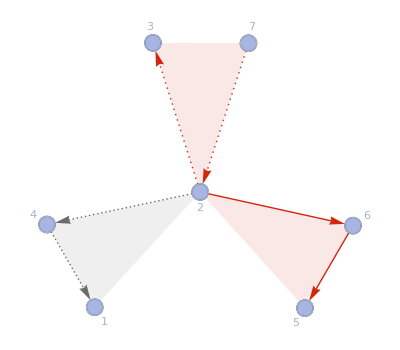
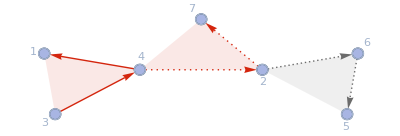

```mathematica
atomPreservingEvolution["EventsStatesPlotsList",VertexLabels->Automatic]
```

```mathematica
atomPreservingEvolution["ExpressionsEventsGraph"]
```

-Graphics-

```mathematica
atomPreservingEvolution["CausalGraph"]
```

-Graphics-

# Creating Atoms

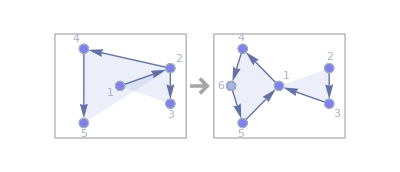

```mathematica
RulePlot[WolframModel[{{1,2,3},{2,4,5}}->{{1,4,6},{2,3,1},{6,5,1}}],VertexLabels->Automatic]
```

```mathematica
growingEvolution = WolframModel[
{{1,2,3},{2,4,5}}->{{1,4,6},{2,3,1},{6,5,1}},
{{1,2,3},{2,4,5},{4,6,7}},
<|"MaxEvents"->50|>]
```

WolframModelEvolutionObject[…]

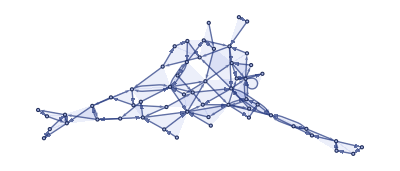

```mathematica
growingEvolution["FinalStatePlot"]
```

```mathematica
growingEvolutionLarge = WolframModel[
{{1,2,3},{2,4,5}}->{{1,4,6},{2,3,1},{6,5,1}},
{{1,2,3},{2,4,5},{4,6,7}},
<|"MaxEvents"->10000|>]
```

WolframModelEvolutionObject[<|Version -> 2, <<7>>, EventGenerations -> {0, 1, 2, 3, 4, 5, 5, 6, 6, 7, 7, 7, 7, 8, 8, 8, 8, 9, 9, 9, 9, 9, 9, 10, 10, 10, 10, 10, 10, 10, 10, 11, 11, 11, 11, 11, 11, 11, 11, 11, 11, 11, 11, 11, 12, 12, 12, 12, 12, 12, 12, 12, 12, <<9922>>, 28, 28, 28, 28, 28, 28, 28, 28, 28, 28, 28, 28, 28, 28, 28, 28, 28, 28, 28, 28, 28, 28, 28, 28, 28, 28}|>]

```mathematica
growingEvolutionLarge["FinalStatePlot"]
```

-Graphics-

# ToPatternRules